```mathematica
SetDirectory[NotebookDirectory[]];
```

31 °

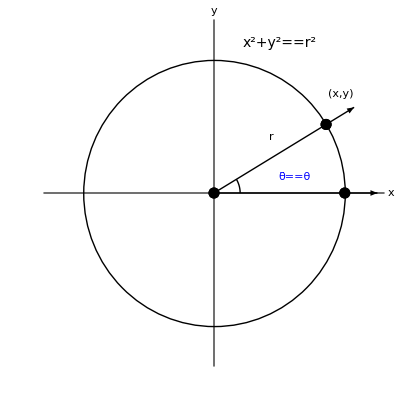

{reference-q1.pdf,reference-q1.svg}

```mathematica
r=4;
θ=121*Degree-90*Degree
Show[
ListPlot[{{r Cos[θ],r Sin[θ]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{r ,0}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{0,0}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Text[Style[HoldForm[r],Large,Italic],{(r+1) Cos[θ]/2-0.4,(r+1) Sin[θ]/2+0.4}]}],
Graphics[{Text[Style["(x,y)",Large,Italic],{(r+1) Cos[θ]-0.4,(r+1) Sin[θ]+0.4}]}],
Graphics[{Text[Style[HoldForm[x^2+y^2==r^2],14,Italic],{2,4.5}]}],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Circle[{0,0},r]}],
Graphics[{Circle[{0,0},0.2r,{0,θ}]}],
Graphics[{Text[Style[HoldForm[θ̄==θ],Blue,Large],{0.2(r+1) Cos[θ/2]+1.5,0.2(r+1) Sin[θ/2]+0.2}]}],
Ticks->None,GridLines->None,
PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export[{"reference-q1.pdf","reference-q1.svg"},%]
```

```mathematica
{"reference-q1.pdf","reference-q1.svg"}
```

121 °

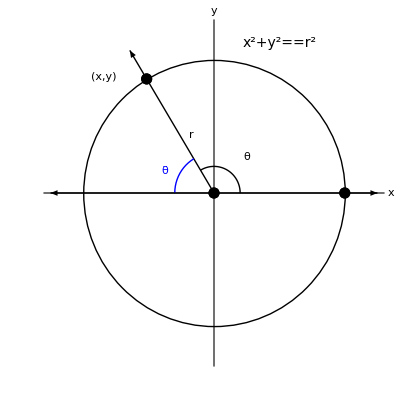

{reference-q2.pdf,reference-q2.svg}

```mathematica
r=4;
θ=121*Degree-0*90*Degree
Show[
ListPlot[{{r Cos[θ],r Sin[θ]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{r ,0}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{0,0}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Text[Style[HoldForm[r],Large,Italic],{(r+1) Cos[θ]/2+0.6,(r+1) Sin[θ]/2-0.4}]}],
Graphics[{Text[Style["(x,y)",Large,Italic],{(r+1) Cos[θ]-0.8,(r+1) Sin[θ]-0.8}]}],
Graphics[{Text[Style[HoldForm[x^2+y^2==r^2],14,Italic],{2,4.5}]}],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Arrow[{{0,0},-{(r+1) ,0}}]}],
Graphics[{Circle[{0,0},r]}],
Graphics[{Circle[{0,0},0.2r,{0,θ}]}],
Graphics[{Blue,Circle[{0,0},0.3r,{θ,Pi}]}],
Graphics[{Text[Style[HoldForm[θ],Large],{0.2(r+1) Cos[θ/2]+0.5,0.2(r+1) Sin[θ/2]+0.2}]}],
Graphics[{Text[Style[HoldForm[θ̄],Blue,Large],-{0.2(r+1) Cos[θ/2]+1,-0.2(r+1) Sin[θ/2]+0.2}]}],
Ticks->None,GridLines->None,
PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export[{"reference-q2.pdf","reference-q2.svg"},%]
```

```mathematica
{"reference-q2.pdf","reference-q2.svg"}
```

211 °

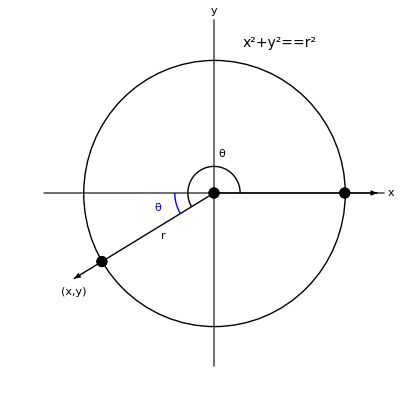

{reference-q3.pdf,reference-q3.svg}

```mathematica
r=4;
θ=121*Degree+1*90*Degree
Show[
ListPlot[{{r Cos[θ],r Sin[θ]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{r ,0}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{0,0}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Text[Style[HoldForm[r],Large,Italic],{(r+1) Cos[θ]/2+0.6,(r+1) Sin[θ]/2}]}],
Graphics[{Text[Style["(x,y)",Large,Italic],{(r+1) Cos[θ],(r+1) Sin[θ]-0.4}]}],
Graphics[{Text[Style[HoldForm[x^2+y^2==r^2],14,Italic],{2,4.5}]}],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Circle[{0,0},r]}],
Graphics[{Circle[{0,0},0.2r,{0,θ}]}],
Graphics[{Blue,Circle[{0,0},0.3r,{Pi,θ}]}],
Graphics[{Text[Style[HoldForm[θ],Large],{0.2(r+1) Cos[θ/2]+0.5,0.2(r+1) Sin[θ/2]+0.2}]}],
Graphics[{Text[Style[HoldForm[θ̄],Blue,Large],-{0.2(r+1) Cos[θ/2]+2,0.2(r+1) Sin[θ/2]-0.5}]}],
Ticks->None,GridLines->None,
PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export[{"reference-q3.pdf","reference-q3.svg"},%]
```

```mathematica
{"reference-q3.pdf","reference-q3.svg"}
```

301 °

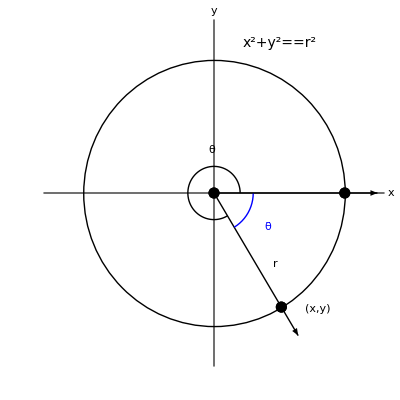

{reference-q4.pdf,reference-q4.svg}

```mathematica
r=4;
θ=121*Degree+2*90*Degree
Show[
ListPlot[{{r Cos[θ],r Sin[θ]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{r ,0}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{0,0}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Text[Style[HoldForm[r],Large,Italic],{(r+1) Cos[θ]/2+0.6,(r+1) Sin[θ]/2}]}],
Graphics[{Text[Style["(x,y)",Large,Italic],{(r+1) Cos[θ]+0.6,(r+1) Sin[θ]+0.8}]}],
Graphics[{Text[Style[HoldForm[x^2+y^2==r^2],14,Italic],{2,4.5}]}],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Circle[{0,0},r]}],
Graphics[{Circle[{0,0},0.2r,{0,θ}]}],
Graphics[{Blue,Circle[{0,0},0.3r,{θ,2Pi}]}],
Graphics[{Text[Style[HoldForm[θ],Large],{0.2(r+1) Cos[θ/2]+0.8,0.2(r+1) Sin[θ/2]+0.8}]}],
Graphics[{Text[Style[HoldForm[θ̄],Blue,Large],{0.2(r+1) Cos[θ/2]+2.5,0.2(r+1) Sin[θ/2]-1.5}]}],
Ticks->None,GridLines->None,
PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export[{"reference-q4.pdf","reference-q4.svg"},%]
```

```mathematica
{"reference-q4.pdf","reference-q4.svg"}
```

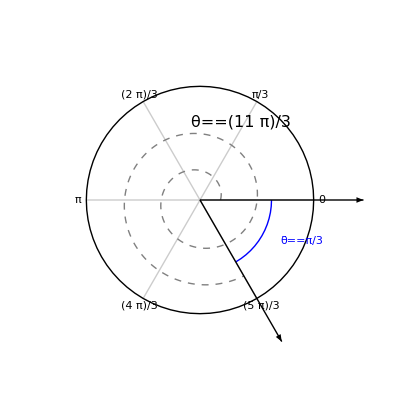

```mathematica
θ=11Pi/3;
Show[PolarPlot[{t/7+0.5},{t,θ,0},PlotStyle->{Thick,Dashed,Gray},Ticks->None,PolarTicks->{Table[i,{i,0,2 Pi-Pi/3,Pi/3}],Automatic},
PolarGridLines->{Table[i,{i,0,2 Pi-Pi/3,Pi/3}],{}},PolarAxes->Automatic],
Graphics[{Text[Style[HoldForm[θ==11Pi/3],16],{1,1.9}]}],
Graphics[{Text[Style[HoldForm[θ̄==Pi/3],Blue,Large],{2.5,-1}]}],
Graphics[{Blue,Thick,Circle[{0,0},1.75,{5Pi/3,2Pi}]}],
Graphics[{Arrow[{{0,0},4{Cos[0],Sin[0]}}]}],
Graphics[{Arrow[{{0,0},4{Cos[θ],Sin[θ]}}]}],
PlotRange->{{-4,4},{-4,4}}]
Export[{"referenceex-1-1.pdf","referenceex-1-1.svg"},%];
```

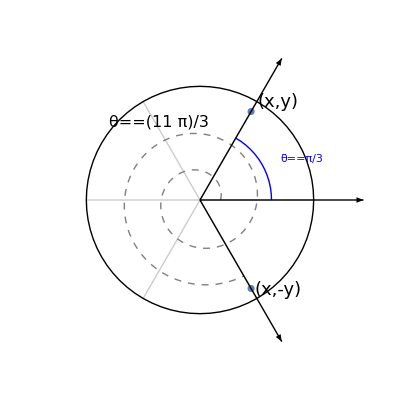

```mathematica
θ=11Pi/3;
Show[PolarPlot[{t/7+0.5},{t,θ,0},PlotStyle->{Thick,Dashed,Gray},Ticks->None,PolarTicks->None,
PolarGridLines->{Table[i,{i,0,2 Pi-Pi/3,Pi/3}],{}},PolarAxes->Automatic],
ListPlot[2.5{{Cos[Pi/3],Sin[Pi/3]},{Cos[5Pi/3],Sin[5Pi/3]}}],
Graphics[{Text[Style[HoldForm[θ==11Pi/3],16],{-1,1.9}]}],
Graphics[{Text[Style[HoldForm[θ̄==Pi/3],Blue,Large],{2.5,1}]}],
Graphics[{Blue,Thick,Circle[{0,0},1.75,{0,Pi/3}]}],
Graphics[{Arrow[{{0,0},4{Cos[0],Sin[0]}}]}],
Graphics[{Arrow[{{0,0},4{Cos[θ],Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},4{Cos[Pi/3],Sin[Pi/3]}}]}],
PlotRange->{{-4,4},{-4,4}},
Epilog->{
Text[Style["(x,y)",18],{1.9,2.4}],
Text[Style["(x,-y)",18],{1.9,-2.2}]
}]
Export[{"referenceex-1-2.pdf","referenceex-1-2.svg"},%];
```